```mathematica
T=(1/2)*l1^2*(Theta1'[t])^2*(m1+m2)+(1/2)*m2*l2^2*(Theta2'[t])^2+m2*l1*l2*Theta1'[t]*Theta2'[t]*Cos[Theta1[t]-Theta2[t]];
V=-(m1+m2)*g*l1*Cos[Theta1[t]]-g*m2*l2*Cos[Theta2[t]];
L=T-V;
(*Parameters for double pendulum*)
l1=1;
l2=1;
g=1;
m1=1;
m2=1;
(*Initial Condtions*)
Mass1x=0;
Mass1v=1.2;
Mass2x=0;
Mass2v=1.2;
(*Run Time*)
StartTime=0;
EndTime=30;
(*Solving for \ddot\theta 1 and 2 *)
eq3=l1*Theta1''[t]*(m1+m2)+m2*l2*Theta2''[t]*Cos[Theta1[t]-Theta2[t]]+m2*l2*(Theta2'[t])^2*Sin[Theta1[t]-Theta2[t]]+(m1+m2)*g*Sin[Theta1[t]] ==0;
```

```mathematica
eq4=m2*l1*Theta1''[t]*Cos[Theta1[t]-Theta2[t]]+m2*l2*Theta2''[t]-m2*l1*(Theta1'[t])^2*Sin[Theta1[t]-Theta2[t]]+g*m2*Sin[Theta2[t]] ==0;
```

```mathematica
solved=Solve[{eq3,eq4},{Theta1''[t],Theta2''[t]}];
```

```mathematica
(*Gotta take the the thetas out of the array they are trapped in*)
```

```mathematica
hi1[t_]=Theta1''[t]/. solved[[1]];
bye1[t_]=Theta2''[t]/. solved[[1]];

(*NDSolve is lovely, this can be subsituted for any other way to solving differential equations, this was just the most convienient option*)
```

```mathematica
s=NDSolve[{Theta1''[t]==hi1[t],Theta2''[t]==bye1[t],Theta1[0]==Mass1x,Theta2[0]==Mass2x,Theta1'[0]==Mass1v,Theta2'[0]==Mass2v},{Theta1,Theta2,Theta1',Theta2'},{t,StartTime,EndTime}];
```

```mathematica
(*This is to present the plot, it turns the output of theta 1 into coordniates*)
```

```mathematica
x1[t_]:=l1*Sin[Theta1[t]]/. s[[1]];
y1[t_]:=-l1*Cos[Theta1[t]]/. s[[1]];
 (*This does the same as above but with theta 2*)
x2[t_]:=l1*Sin[Theta1[t]]+l2*Sin[Theta2[t]]/. s[[1]];
y2[t_]:=-l1*Cos[Theta1[t]]-l2*Cos[Theta2[t]]/. s[[1]];
(*This is getting theta 1 and 2 out of the array so I can use them to make a phase plot *)
Omega1[t_]:=Theta1[t]/.s[[1]];
Omega2[t_]:=Theta2[t]/.s[[1]];

(*This is the plot for the double pendulum, its pretty cool*)
Plot1=Animate[Graphics[{Thick,(*This is the line attached to origin and mass 1*)Line[{{0,0},{x1[q],y1[q]}}],(*This is the line attached to mass 1 and mass 2*)Line[{{x1[q],y1[q]},{x2[q],y2[q]}}],(*mass 1*) {Red,Disk[{x2[q],y2[q]},0.05]},(*mass 2*) {Blue,Disk[{x1[q],y1[q]},0.05]},{Gray,Line[Table[{x2[t],y2[t]},{t,0,q,0.02}]]} (*trail*)},PlotRange->{{-2.5,2.5},{-2.5,2.5}},Axes->True,Frame->True,FrameTicks->Automatic,ImageSize->Large,GridLines->Automatic],{q,StartTime,EndTime}];
```

```mathematica
(*THis is the plot that makes the animates phase diagram*)
```

```mathematica
Plot2=Animate[Graphics[{{Red,Disk[{Omega1[q],Omega2[q]},0.1]},{Gray,Line[Table[{Omega1[t],Omega2[t]},{t,0,q,0.02}]]} (*trail*)},PlotRange->{{-15,15},{-15,15}},Axes->True,Frame->True,FrameTicks->Automatic,ImageSize->Large,GridLines->Automatic],{q,StartTime,EndTime}];

(*Phase Diagram Stationary*)
```

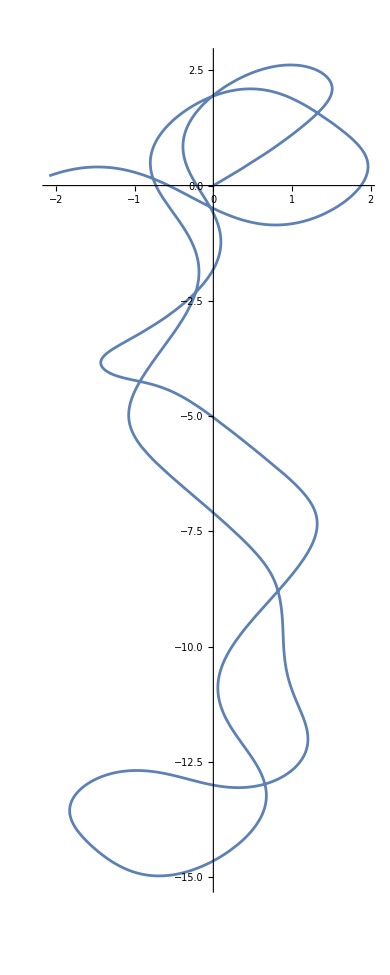

```mathematica
ParametricPlot3D[{Theta1'[t]-Theta2'[t],Theta1[t]-Theta2[t],L}/.s,{t,StartTime,EndTime},PlotRange->All];
ParametricPlot[{Theta1'[t]-Theta2'[t],Theta1[t]-Theta2[t]}/.s,{t,StartTime,EndTime},PlotRange->All];
ParametricPlot[{Theta1'[t],Theta2'[t]}/.s,{t,StartTime,EndTime},PlotRange->All];
ParaPlot=ParametricPlot[{Theta1[t],Theta2[t]}/.s,{t,StartTime,EndTime},PlotRange->All]
ParametricPlot[{T,V}/.s,{t,StartTime,EndTime},PlotRange->All];
```

```mathematica
(*Makes the side by side video*)
OhMyGodPleaseNoCrash=Manipulate[GraphicsRow[{Graphics[{Thick,Line[{{0,0},{x1[q],y1[q]}}],Line[{{x1[q],y1[q]},{x2[q],y2[q]}}],(*First mass*) {Red,Disk[{x2[q],y2[q]},0.05]},(*Second mass*) {Blue,Disk[{x1[q],y1[q]},0.05]},{Gray,Line[Table[{x2[t],y2[t]},{t,0,q,0.02}]]} (*trail*)},PlotRange->{{-2.5,2.5},{-2.5,2.5}},Axes->True,Frame->True,FrameTicks->Automatic,ImageSize->Large,GridLines->Automatic],Graphics[{{Red,Disk[{Omega1[q],Omega2[q]},0.1]},{Gray,Line[Table[{Omega1[t],Omega2[t]},{t,0,q,0.02}]]} (*trail*)},PlotRange->{{-2,2},{-2,2}},Axes->True,Frame->True,FrameTicks->Automatic,ImageSize->Large,GridLines->Automatic]}],{q,StartTime,EndTime}]
```

```mathematica
Export["HighEnergySolutions.mov",OhMyGodPleaseNoCrash];
```